```mathematica
<<Local`QFTToolKit`
DefineTensorShortcuts[{{Q},1},{{σ},4}]
QCDBaseIndices
DefineDottedIndices
```

{{0,1,2,3},{field,{1,2,3,4}},{feyn,{1,2,3,4,5}},{space,{1,2,3}},{timespace,{0,1}},{groupR,{1,2,3}},{gaugeG,{1,2,3,4,5,6,7,8}},{color,{1,2,3}},{flavor,{1,2,3,4,5,6}},{family,{1,2,3}}}

```mathematica
DefineTensorShortcuts[{{η,t,δ,ε,λ,D,F},1},
{{y,U,u},2},
{{σ,λ},3}
]
```

Lecture 16 Sept 2011

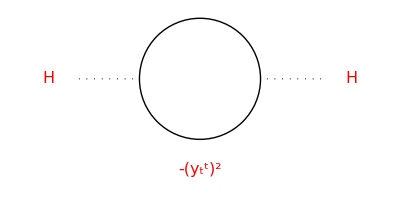
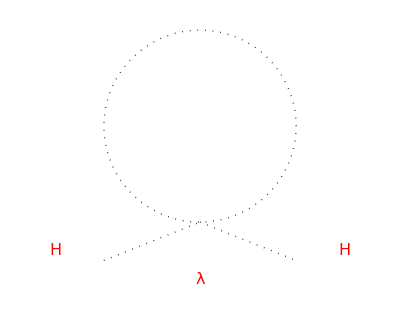
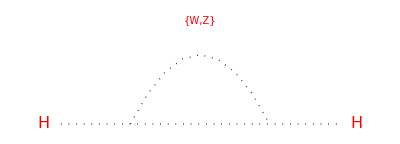
Some problems with the Standard Model lagrangian in that it predicts quadratic divergences from higher order Higgs mass terms which require fine tuning to cancel:ℒ→μ^2 H^†.H+λ (H^†.H)^2 with diagrams -Graphics- and -Graphics- and -Graphics-
Possible solutions: ()cancelation of quadradic terms, ()Higgs not fundamental [other diagrams], ()no Higgs.

```mathematica
scale=1;
MidArrow[xy_]:={Arrow[{xy[[1]],(xy[[1]]+xy[[2]])/2}],Line[{(xy[[1]]+xy[[2]])/2,xy[[2]]}]};
TextOver[text_,xy_]:={White,Disk[xy,0.2scale],
Text[Style[text,FontSize->16,Red],xy]};
Graphics121[x_]:=Graphics[{Thick,Black,
Circle[{0,0},scale],
Dotted,Line[{{-2 scale,0},{-1 scale,0}}],
Line[{{2 scale,0},{1 scale,0}}],
TextOver[x,{0,-1.3 scale}]
}
];
Graphics121[x_,x0_,x1_]:=Graphics[{Thick,Black,
Circle[{0,0},scale],
Dotted,Line[{{-2 scale,0},{-1 scale,0}}],
Line[{{2 scale,0},{1 scale,0}}],
TextOver[x,{0,-1.5scale}],
TextOver[x0,{-2.5,0}],TextOver[x1,{2.5,0}]
}
];
Graphics20[x_]:=Graphics[{Thick,Black,Dotted,
Circle[{0,0},scale],
Line[{{-scale,-1.2 scale},{ 0,-scale}}],
Line[{{0,-scale},{ scale,-1.6 scale}}],
TextOver[x,{0,-1.3 scale}]
}
];
Graphics20[x_,x0_,x1_]:=Graphics[{Thick,Black,Dotted,
Circle[{0,0},scale],
Line[{{-scale,-1.4 scale},{ 0,-scale}}],
Line[{{0,-scale},{ scale,-1.4scale}}],
TextOver[x,{0,-1.6 scale}],
TextOver[x0,{-1.5,-1.3}],TextOver[x1,{1.5,-1.3}]
}
];
Graphics12d1[x_,x0_,x1_]:=Graphics[{Thick,Black,Dotted,
Line[{{-4 ,0},{4 ,0}}],
BezierCurve[{{-2,0},{0,4},{2,0}}],
TextOver[x,{0,3. },10],
TextOver[x0,{-4.5,0}],TextOver[x1,{4.5,-0}]
}
];
PR1["Some problems with the Standard Model lagrangian in that it predicts quadratic divergences from higher order Higgs mass terms which require fine tuning to cancel:",
ℒ->μ μ SuperDagger[H].H+λ (SuperDagger[H].H)^2," with diagrams ",
Graphics121[-yd[t]^2,H,H],and,
Graphics20[λ,H,H],and,
Graphics12d1[{W,Z},H,H],
NL,"Possible solutions: ()cancelation of quadradic terms, ()Higgs not fundamental [other diagrams], ()no Higgs. "
];
```

```mathematica
PR1["Chiral Super Field symbolically indicated by ",ϕd[i]∈{Ad[i]←"scalar",ψd[i]←"fermion",Fd[i]←"auxiliary"}," where the index i accounts different multiplets. The Lagrangian consists of two parts: the Kahler potential and the superpotential. The Kahler potential consists of the kinetic terms ",
tmpKin=Subscript[ℒ, kin]->xPartialD[SuperStar[Ad[i]],μ]xPartialDu[Ad[i],μ]+OverBar[ψd[i]]. I γu[μ].xPartialD[ψd[i],μ]+SuperStar[Fd[i]] Fd[i],
NL,"The superpotential is defined by a function ",W[ϕd[i_]],yield,
tmpLW=Subscript[ℒ, W]->-1/2 xPartialD[W,{ϕd[i]->Ad[i],ϕd[j]->Ad[j]}].ψu[i].ψu[j]+xPartialD[W,{ϕd[i]->Ad[i]}].Fd[i],
NL,"The Euler-Lagrange equation for ",Fd[i]->-xPartialD[W,{ϕd[i]->Ad[i]}],
NL,"Eliminating F ",yield,tmpL=ℒ⊃-Subscript[V, F]->-Abs[xPartialD[W,{ϕd[i]->Ad[i]}]]^2,CR["←The F's in the Lagrangian seem to cancel. Where does V_F fit in?"]
]
```

Chiral Super Field symbolically indicated by ϕ_i^i∈{A_i^i←scalar,ψ_i^i←fermion,F_i^i←auxiliary} where the index i accounts different multiplets. The Lagrangian consists of two parts: the Kahler potential and the superpotential. The Kahler potential consists of the kinetic terms ℒ_kin→OverBar[ψ_i^i].ⅈ γ_μ^μ.UnderBar[∂]_μ[ψ_i^i]+(F_i^i)^* F_i^i+UnderBar[∂]_μ[(A_i^i)^*] UnderBar[∂]^μ[A_i^i]
The superpotential is defined by a function W[ϕ_i_^i_] ⟶ ℒ_W→UnderBar[∂]_{ϕ_i^i→A_i^i}[W].F_i^i-1/2 UnderBar[∂]_{ϕ_i^i→A_i^i,ϕ_j^j→A_j^j}[W].ψ_i^i.ψ_j^j
The Euler-Lagrange equation for F_i^i→-UnderBar[∂]_{ϕ_i^i→A_i^i}[W]
Eliminating F  ⟶ ℒ⊃-V_F→-Abs[UnderBar[∂]_{ϕ_i^i→A_i^i}[W]]^2←The F's in the Lagrangian seem to cancel. Where does V_F fit in?

```mathematica
PR1["Introduce gauge field kinetic term: ",(*(16)*)
tmpLg=Subscript[ℒ, gauge]->-1/4 Fdd[μ,υ]+OverBar[λu[a]].I Slash[D].λu[a]+1/2 Du[a].Du[a], " where ",NL,
{λ,Ad[μ],D}->{"Weyl fermion(gaugino)","vector gauge field","auxiliary field"}//ColumnForms
];
```

Introduce gauge field kinetic term: ℒ_gauge→OverBar[λ_a^a].ⅈ (/D).λ_a^a+1/2 D_a^a.D_a^a-F_μυ^μυ/4 where 
λ
A_μ^μ
D→Weyl fermion(gaugino)
vector gauge field
auxiliary field

Lecture notes direct copy

```mathematica
PR1["Left Chiral Super Field can be written: ",ϕd[i]->Ad[i]+θ ψd[i]+θ.θ Fd[i],NL,
"The super potential: ",W[ϕd[i]]->Mdd[i,j].ϕd[i].ϕd[j]+λddd[i,j,k].ϕd[i].ϕd[j].ϕd[k],NL,
"where ",
OBd[D,d1@α].W[ϕd[i]]->0,NL,
"The kinetic terms in the Lagrangian: ",
tmpKin=Subscript[ℒ, kin]->xPartialDu[SuperDagger[Ad[i]],μ].xPartialD[Ad[i],μ]+ψd[i]. (I σu[μ]).xPartialD[OverBar[ψd[i]],μ]+SuperDagger[Fd[i]]. Fd[i],NL,
Subscript[ℒ, kin]->{SuperDagger[ϕd[i]].ϕd[i]↤θ θ θ̄ θ̄}->xPartialDu[SuperDagger[Ad[i]],μ].xPartialD[Ad[i],μ]
];
```

Left Chiral Super Field can be written: ϕ_i^i→A_i^i+θ.θ F_i^i+θ ψ_i^i
The super potential: W[ϕ_i^i]→M_ij^ij.ϕ_i^i.ϕ_j^j+λ_ijk^ijk.ϕ_i^i.ϕ_j^j.ϕ_k^k
where (D̄)_(α̇)^(α̇).W[ϕ_i^i]→0
The kinetic terms in the Lagrangian: ℒ_kin→(F_i^i)^†.F_i^i+UnderBar[∂]^μ[(A_i^i)^†].UnderBar[∂]_μ[A_i^i]+ψ_i^i.(ⅈ σ_μ^μ).UnderBar[∂]_μ[OverBar[ψ_i^i]]
ℒ_kin→{(ϕ_i^i)^†.ϕ_i^i↤θ^2 (θ̄)^2}→UnderBar[∂]^μ[(A_i^i)^†].UnderBar[∂]_μ[A_i^i]

```mathematica
PR1["To go from SM to SUSY: ",{q,u,d,l,e}->SuperFields[Q,U,D,L,e]," we use prescription ",
q⟶{Q->Ad[Q]+θ ψd[Q]+θ.θ Fd[Q]}," where ",{Ad[Q], ψd[Q], Fd[Q]}->{q̃[superpartner],q[fermionfield],Fd[q][auxfield]}//ColumnForms
]
PR1["For higgs to superhiggs: ",h⟶{H->h+θ h̃+θ.θ.Fd[H]}," where ",(H->{{hu[0]},{hu["-"]}})//MatrixForms,
NL,"If ",l̃==h," lepton number would be violated."
]
```

To go from SM to SUSY: {q,u,d,l,e}→SuperFields[Q,U,D,L,e] we use prescription q⟶{Q→A_Q^Q+θ.θ F_Q^Q+θ ψ_Q^Q} where A_Q^Q
ψ_Q^Q
F_Q^Q→q̃[superpartner]
q[fermionfield]
F_q^q[auxfield]

For higgs to superhiggs: h⟶{H→h+θ.θ.F_H^H+θ h̃} where H→(h_0^0
h_-^-)
If l̃==h lepton number would be violated.

```mathematica
PR1["The prescription for getting a SUSY lagrangian from the SM is changing the SM fields with SuperFields, for example, ",
Subscript[ℒ, SM]==qd[i].ydd[i,j].uud[c,j].h⟶Subscript[ℒ, SUSY]->Qd[i].ydd[i,j].Uud[c,j].H,NL,
"The coupling constants are extracted by comparing W_int with SM terms. For example, the potential term, ",
tmp=W->OverTilde[qd[i]].ydd[i,j].uud[c,j].h ," would yield the coefficient: ",
tmp= xPartialD[W^2,{OverTilde[qd[i]],uud[c,j]}]->ydd[i,j].h,
NL,"multiplying by corresponding superpartners of the derivatives yield the SUSY interaction term: ",
qd[i].tmp[[2]].Tensor[ũ,{c,Void},{Void,j}],
NL,"The SUSY lagrangian for the ",ydd[i,j]," coupling cooresponds to 3 diagrams: ",
," where the vertex has 2 fermions and 1 scalar of the possible interacting superfields. "
];
```

The prescription for getting a SUSY lagrangian from the SM is changing the SM fields with SuperFields, for example, ℒ_SM==q_i^i.y_ij^ij.u_cj^cj.h⟶ℒ_SUSY→Q_i^i.y_ij^ij.U_cj^cj.H
The coupling constants are extracted by comparing W_int with SM terms. For example, the potential term, W→OverTilde[q_i^i].y_ij^ij.u_cj^cj.h would yield the coefficient: UnderBar[∂]_{OverTilde[q_i^i],u_cj^cj}[W^2]→y_ij^ij.h
multiplying by corresponding superpartners of the derivatives yield the SUSY interaction term: q_i^i.y_ij^ij.h.(ũ)_cj^cj
The SUSY lagrangian for the y_ij^ij coupling cooresponds to 3 diagrams: Null where the vertex has 2 fermions and 1 scalar of the possible interacting superfields.